噗 经济班2017.9班聚超科学分组方法！

p.s.1. 已经为图中关系隐去姓名；

```mathematica
relation[x_]:=x[[1]]->#&/@x[[2;;]]
originaldata=Import["~/Desktop/经济班班聚科学分组/16_16_2.xls"][[2]];
nameList =Import["~/Desktop/经济班班聚科学分组/list.xlsx"][[1]];
placeRule = Apply[IntegerPart[#2]-> #1&, #]&/@nameList;
genderRule1 = Apply[#1-> #3&, #]&/@nameList;
genderRule2 = {("男"->"女") -> 2, ("女"->"男")->2, ("男"->"男")->-1, ("女"->"女")->1};
dataclean[x_]:=Select[If[#==1,IntegerPart[x[[#]]], If[ x[[#]]==1, #-1,0]]&/@Range[32],
#≠ 0&]
```

```mathematica
cleanedData = dataclean/@originaldata /. placeRule;
relations = Flatten[relation/@cleanedData];
genderWeights = relations /.genderRule1 /. genderRule2;
```

```mathematica
relations = Graph[relations]
```

-Graphics-

这里是找到的社区团（不平均）

```mathematica
communities =FindGraphCommunities[relations,
Method->"Modularity"]
```

```mathematica
CommunityGraphPlot[
relations,
communities]
```

-Graphics-

这里是找到的三组社区团（平均分配）

```mathematica
FindGraphPartition[relations,3]
```

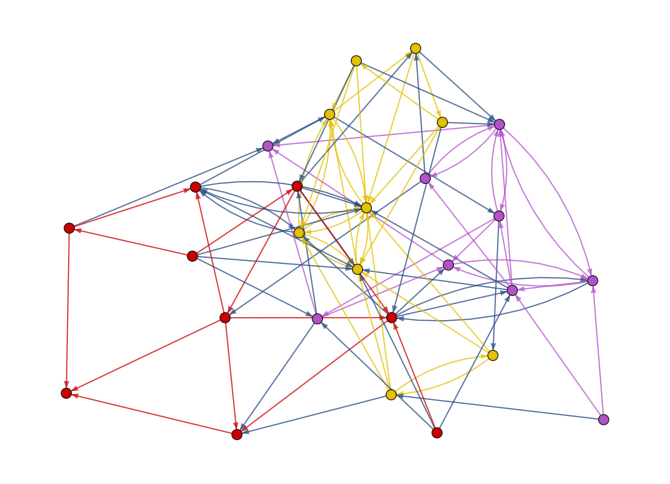

```mathematica
HighlightGraph[relations,
 Subgraph[relations, #]&/@FindGraphPartition[relations,3]]
```

这里是找到的四组社区团（平均分配）

```mathematica
FindGraphPartition[relations,4]
```

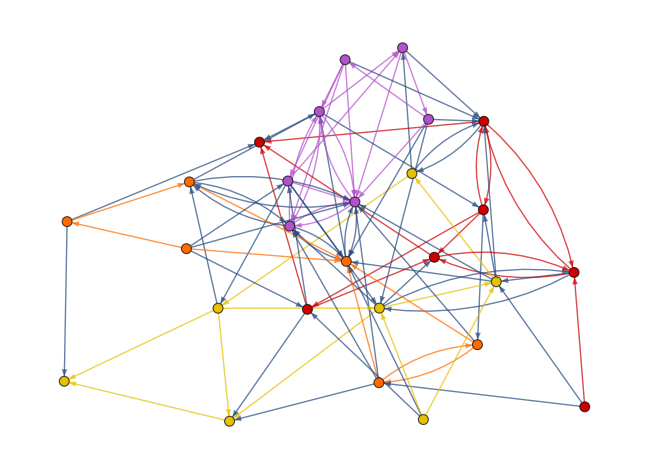

```mathematica
HighlightGraph[relations, 
Subgraph[relations, #]&/@FindGraphPartition[relations,4]]
```